```mathematica
Guy F. Mongelli                        11/3/2012
Prof. J. Adin Mann                  ECHE 475
```

```mathematica
Midterm Take Home Problem Set
```

```mathematica
Problem 1
```

```mathematica
Part A:
```

```mathematica
The following is a parametrically defined vector valued function (Rank 1).  The parameter variable, t, is a scalar which is varied in the domain of [0,π/2].  Therefore the codomain of x is identically [0,π/2].The codomain of y is [0,1].  The x and y components of this parameterized function are continuous on the domain of t ( and even in extended domains of [-∞,∞]).  The function is also infinitely differentiable in the bounded and infinite limits of t.  Although, only the first two derivatives are of interest because after the first derivative the x-component (first element) goes to zero with respect to time.  The x component will have issues after the first derivative because the function will be undefined as all of the y values will be mapped onto the x=0 ordinate. Because of their defferentiability properties, the elements of the vector valued function are also square integrable functions.
```

```mathematica
y1=({{t}, {(Sin[t])^2}})
```

{{t},{Sin[t]^2}}

```mathematica
N[Pi/2,3]
```

1.57

```mathematica
FindMaximum[(Sin[t])^2,t]
```

{1.,{t→1.5708}}

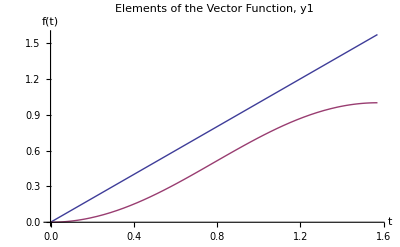

```mathematica
Plot[{t,(Sin[t])^2},{t,0,Pi/2},PlotLabel->"Elements of the Vector Function, y1",AxesLabel->{t,f[t]}]
```

```mathematica
For interest, the length of the vector as a function of time is:
```

```mathematica
dist[t_]=Sqrt[t^2+(Sin[t])^4]
```

√(t^2+Sin[t]^4)

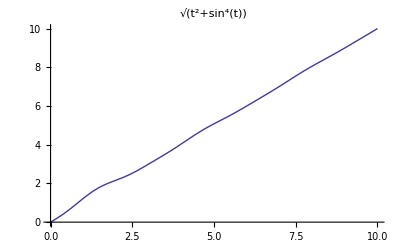

```mathematica
Plot[dist[t],{t,0,10},PlotLabel->dist[t]]
```

```mathematica
dist[Pi/2]
```

√(1+π^2/4)

```mathematica
N[dist[Pi/2],3]
```

1.86

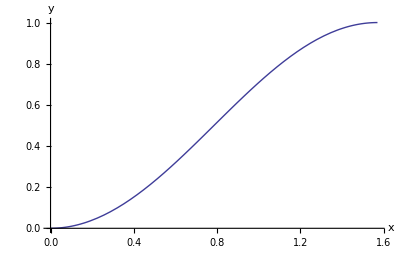

```mathematica
ParametricPlot[{t,(Sin[t])^2},{t,0,Pi/2},AxesLabel->{x,y}]
```

```mathematica
To see how this mapping changes as the exponent on t in the first element is varied, see the following plot:
```

```mathematica
Manipulate[ParametricPlot[{t^n
,(Sin[t])^2},{t,0,Pi/2},PlotRange->{0,1},AxesLabel->{x,y}],{n,1,2,3,4,5}]
```

```mathematica
The following function is a scalar function (Rank 0 tensor).  The domain is from [0,1].  The codomain is from [0,1]. The function is continuous over the domain and extended domain([-∞,∞]).  The function is smooth and infinitely differentiable .  It is also square integrable.
```

```mathematica
y2=x^2
```

x^2

```mathematica
The domain of this function is [0,1] and the codomain is [0,1].
```

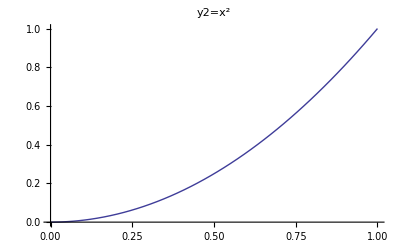

```mathematica
Plot[y2,{x,0,1},PlotLabel->"y2=x^2"]
```

```mathematica
Part B:
```

```mathematica
Strange[x_]=(Sin[x]+Cos[x]+Exp[x])/Log[1+x^2]
```

(ⅇ^x+Cos[x]+Sin[x])/Log[1+x^2]

```mathematica
Strange[0]
```

Power::infy: Infinite expression 1/0 encountered.

ComplexInfinity

```mathematica
The notion of complex intinity alludes to the idea that mathematica is not sure which portions (phases/phasors)of the infinite limit are in the real plane and which are in the complex plane.
```

```mathematica
The function is not defined at the origin, otherwise the limit would be relatively simple to compute.   The derivatives via the quotient rule and L'Hospital's rule are not helpful in solving this problem.
```

```mathematica
D[(Sin[x]+Cos[x]+Exp[x])/Log[1+x^2],x]
```

(ⅇ^x+Cos[x]-Sin[x])/Log[1+x^2]-(2 x (ⅇ^x+Cos[x]+Sin[x]))/((1+x^2) Log[1+x^2]^2)

```mathematica
For interest into the true derivative of the function, it is computed here, although it does not assist in solving this problem.
```

```mathematica
Expand[D[(Sin[x]+Cos[x]+Exp[x])/Log[1+x^2],x]]
```

-(2 ⅇ^x x)/((1+x^2) Log[1+x^2]^2)-(2 x Cos[x])/((1+x^2) Log[1+x^2]^2)+ⅇ^x/Log[1+x^2]+Cos[x]/Log[1+x^2]-(2 x Sin[x])/((1+x^2) Log[1+x^2]^2)-Sin[x]/Log[1+x^2]

```mathematica
Full Simplify[D[(Sin[x]+Cos[x]+Exp[x])/Log[1+x^2],x]]
```

1/(Log[1+x^2]^2)Full (Log[1+x^2] (ⅇ^x+Cos[x]-Sin[x])-(2 x (ⅇ^x+Cos[x]+Sin[x]))/(1+x^2))

```mathematica
Limit[D[(Sin[x]+Cos[x]+Exp[x])/Log[1+x^2],x],x->0]
```

-∞

```mathematica
Finally, the L'Hospital derivative is computed.   Again it is not helpful, but I  have some interest in seeing what types of information it provides when the L'Hopital's criterion are satisfied versus when they are not.
```

```mathematica
D[Sin[x]+Cos[x]+Exp[x],x]/D[Log[1+x^2],x]
```

((1+x^2) (ⅇ^x+Cos[x]-Sin[x]))/(2 x)

```mathematica
Expand[D[Sin[x]+Cos[x]+Exp[x],x]/D[Log[1+x^2],x]]
```

ⅇ^x/(2 x)+(ⅇ^x x)/2+Cos[x]/(2 x)+1/2 x Cos[x]-Sin[x]/(2 x)-1/2 x Sin[x]

```mathematica
FullSimplify[D[Sin[x]+Cos[x]+Exp[x],x]/D[Log[1+x^2],x]]
```

((1+x^2) (ⅇ^x+Cos[x]-Sin[x]))/(2 x)

```mathematica
Limit[D[Sin[x]+Cos[x]+Exp[x],x]/D[Log[1+x^2],x],x->0]
```

∞

```mathematica
The function is plotted and verifys the limit.
```

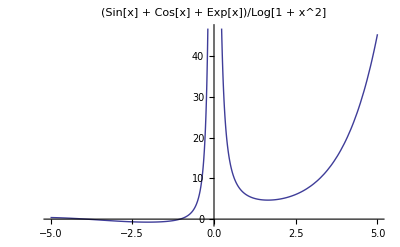

```mathematica
Plot[(Sin[x]+Cos[x]+Exp[x])/Log[1+x^2],{x,-5,5},PlotLabel->"(Sin[x] + Cos[x] + Exp[x])/Log[1 + x^2]"]
```

```mathematica
To find the roots of this function:
```

```mathematica
Solve[(Sin[x]+Cos[x]+Exp[x])/Log[1+x^2]==0,x,Reals]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[(ⅇ^x+Cos[x]+Sin[x])/Log[1+x^2]==0,x,Reals]

```mathematica
NSolve[(Sin[x]+Cos[x]+Exp[x])/Log[1+x^2]==0,x,Reals]
```

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

NSolve[(ⅇ^x+Cos[x]+Sin[x])/Log[1+x^2]==0,x,Reals]

```mathematica
Perhaps expanding the equation out into terms will help:
```

```mathematica
Expand[(Sin[x]+Cos[x]+Exp[x])/Log[1+x^2]]
```

ⅇ^x/Log[1+x^2]+Cos[x]/Log[1+x^2]+Sin[x]/Log[1+x^2]

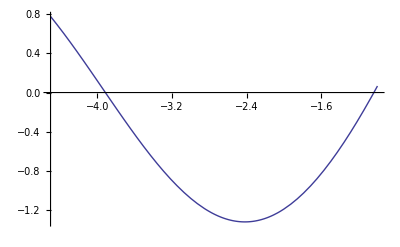

```mathematica
Plot[Sin[x]+Cos[x]+Exp[x],{x,-4.5,-1}]
```

```mathematica
WeirdNum[x_]=Sin[x]+Cos[x]+Exp[x]
```

```mathematica
ⅇ^x+Cos[x]+Sin[x]
```

```mathematica
N[WeirdNum[-1.038434],3]
```

-0.0000316426

```mathematica
N[WeirdNum[-3.9128555],3]
```

-6.33426×10^-6

```mathematica
NSolve[Sin[x]+Cos[x]+Exp[x]==0,x]
```

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

NSolve[ⅇ^x+Cos[x]+Sin[x]==0,x]

```mathematica
Limit[(Sin[x]+Cos[x]+Exp[x])/Log[1+x^2],x->0]
```

∞

```mathematica
The left-hand limit is:
```

```mathematica
Limit[(Sin[x]+Cos[x]+Exp[x])/Log[1+x^2],x->0,Direction->1]
```

∞

```mathematica
The right-hand limit is:
```

```mathematica
Limit[(Sin[x]+Cos[x]+Exp[x])/Log[1+x^2],x->0,Direction->-1]
```

∞

```mathematica
Looking at a plot of this function and evaluating the left and right hand limits indicated that the limit diverges to positive infinity (does not exist).  This comes from the misbehavior of the logarithm in the denominator around x=0.
```

```mathematica
To verify the [mis]behavior of each fundamental function, they are plotted below.
```

```mathematica
<<PlotLegends`
```

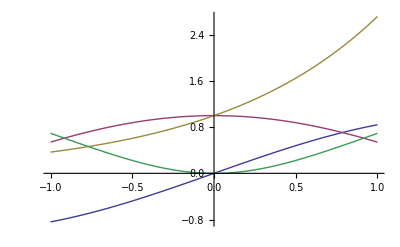

```mathematica
Plot[{Sin[x],Cos[x],Exp[x],Log[1+x^2]},{x,-1,1},PlotLegend->{"Sin[x]","Cos[x]","Exp[x]","Log[1+x^2]"}]
```

```mathematica
Part C:
```

```mathematica
The infinite product can be rewritten as:
```

```mathematica
∏_(n=1)^∞ (2n-1)/(2n)
```

0

```mathematica
The correct way to discuss the infinite product in this context is to say that the infinite product diverges to zero.
```

```mathematica
To understand why this is the case, a careful examination of the value of each term is required.  The integer values on n in the following plot are the most critical.  The funcion starts by generating (1/2) and multiplying it by (3/4), then (5/6) then (7/8), and so on.
```

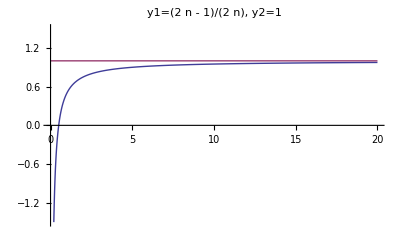

```mathematica
Plot[{(2n-1)/(2n),1},{n,0,20},PlotRange->{-1.5,1.5},PlotLabel->"y1=(2  n - 1)/(2  n), y2=1" ]
```

```mathematica
A method to rewrite the infinite product of a certain number of terms is to recall the gamma function.  Relating the gamma function to the infinte product is fascinating because it reiterates the connection of the integral convergence tests for series.  This infinite product can be rewritten as an infinite series.
```

```mathematica
f[x_]=∏_(n=1)^x (2n-1)/(2n)
```

Gamma[1/2+x]/(√π Gamma[1+x])

```mathematica
When each term is multiplied by successive terms, which are larger, the number decreases and in the infinte limit goes to zero.  This sysstem is analogous to the problem of being 1 foot away from the wall and sequentially taking steps equal to half of the distance remaining from you to the wall to get to the wall.  In any finite limit, it seems that you will never reach the wall, however in the infinite limit, you do.  This infinite product represents the same problem by using multiplication to relate the distance you step as a certain fraction of the distance of the last step.  These steps are getting smaller and smaller, as the distance from the final destination gets smaller and smaller as well.  In essence the infinite product tells you how far you are from the wall (1-partial pruduct) and tells you how far you have left (partial product). In this example the distance stepped is not the same fraction of the distance taken in the last step. Another way to think about it is to consider that even though the numbers multiplied in each term are getting larger, there are an infinite number of fractions less than one being mutiplied by one another. It is not terribly surprising, then that the product of this infinite set of numbers is close enought to zero to call it just that.
```

```mathematica
Limit[Gamma[1/2+x]/(√π Gamma[1+x]),x->∞]
```

0

```mathematica
If it were a series that summed to zero, it would converge to zero, however, based upon my readings most mathematicians would say that the infinite produce diverges to zero.
```

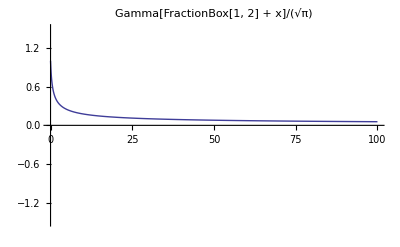

```mathematica
Plot[Gamma[1/2+x]/(√π Gamma[1+x]),{x,0,100},PlotRange->{-1.5,1.5},PlotLabel->"Gamma[FractionBox[1, 2] + x]/(√π)"]
```

```mathematica
The convergence criteria for the infinite product is that the infinite product of a series term denoted a[n] will converge if and only of the infinite series sum of the logarithm of a[n] with base ten converges.
```

```mathematica
∑_(n=1)^∞ Log[(2n-1)/(2n)]
```

Sum::div: Sum does not converge.

∑_(n=1)^∞ Log[(-1+2 n)/(2 n)]

```mathematica
∑_(n=1)^∞ Log[10,(2n-1)/(2n)]
```

Sum::div: Sum does not converge.

∑_(n=1)^∞ Log[(-1+2 n)/(2 n)]/Log[10]

```mathematica
Since these inifinite series sums do not converge (even if only one is sufficient,since it implies the other), we would expect the appropriate manipulation of the infinite product not to converge.
```

```mathematica
In the infinite limit, each successive multiplication step is multiplying by a number that is approxamately 1.
```

```mathematica
Limit[(2n-1)/(2n),n->∞]
```

1

```mathematica
In the infinite series case, each term essentially adds zero to the total sum.
```

```mathematica
Limit[Log[(2n-1)/(2n)],n->∞]
```

0

```mathematica
Limit[(2n-1)/(2n),n->0]
```

-∞

```mathematica
Limit[(2n)/(2n+1),n->0]
```

0

```mathematica
Limit[Log[(2n+1)/(2n)],n->0]
```

∞

```mathematica
Problem 2:
```

```mathematica
Part A:
```

```mathematica
The function is plotted before the limit is evaluated.The existence of the function at the point in the limit of evaluation exists.  Since the right hand and left hand limits exist and equal the same value, the limit is said to exist and go to 1.
```

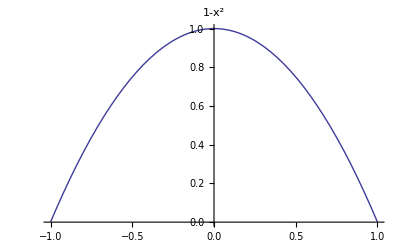

```mathematica
Plot[1-x^2,{x,-1,1},PlotLabel->"1-x^2"]
```

```mathematica
Limit[1-x^2,x->0]
```

1

```mathematica
Limit[1-x^2,x->0,Direction->1]
```

1

```mathematica
Limit[1-x^2,x->0,Direction->-1]
```

1

```mathematica
Part B:
```

```mathematica
The function is plotted.  This goes back to the notion of taking steps toward an wall a certain fixed distance away, where the legnth of the step is proportional to either the distnace travelled or to the distance remaining.  These cases will show that the relationship between the distance taken in a step to the distance travelled, the distance taken in the last step or the distance remaining is not the same.
```

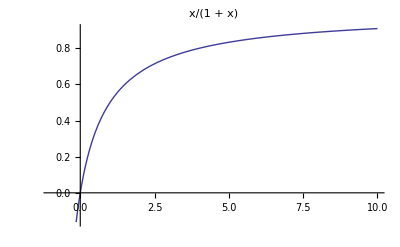

```mathematica
Plot[x/(1+x),{x,-1,10},PlotLabel->"x/(1 + x)"]
```

```mathematica
The function does not posses and discontinuities, lack of smoothness or other misbehavior that would indicate that its limit does not exist. The plot above shows readily that the limit is 1.This limit is important for solving Part C of Problem 3.
```

```mathematica
Limit[x/(1+x),x->∞]
```

1

```mathematica
Part C:
```

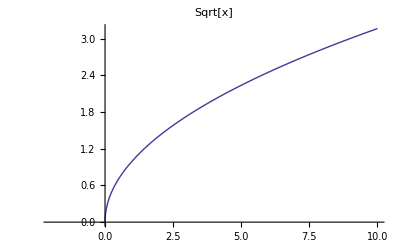

```mathematica
Plot[Sqrt[x],{x,-2,10},PlotLabel->"Sqrt[x]"]
```

```mathematica
The function is plotted above, and is not definted in the real plane for negative values.  The right hand limit is obviously zero, however, the left hand limit is non-obviously zero, and the limit is actually zero.  The problem in part D is more confusing, at least initially, because it also involves square roots in domains that lie along the complex plane.
```

```mathematica
The purpose of the next several plots is to demonstrate the stability as you approach the left hand limit in the above case from the cmoplex plane.  The z=0 plane is shown such that the nullity of the real and complex planes can be determined.  Seating the real and imaginary plots with the z=0 plane shows the instability that occurs as the real plane is approached.  The limit is not defined because it could be from an infinite number of trajectories so approaching it from the real plane gives the limit as complex infiniti.  This is demonstrated in Mathematica in the following cells.
```

```mathematica
Plot3D[{Re[(a+b*I)^2]},{a,-5,5},{b,-5,5},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
This plot shows the real part of an imaginary number squared, where a is the real part of the unsquared imaginary number and b is the complex part of the unsquared imaginary number.
```

```mathematica
Plot3D[{Re[(a+b*I)^2],0},{a,-5,5},{b,-5,5},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
This shows the imaginary component of a functions squared as a function of the real and imaginary parts.
```

```mathematica
Plot3D[{Im[(a+b*I)^2]},{a,-5,5},{b,-5,5},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Plot3D[{Im[(a+b*I)^2],0},{a,-5,5},{b,-5,5},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
The real and imaginary parts of the complex number squared as well as the z=0 plane.
```

```mathematica
Plot3D[{Re[(a+b*I)^2],Im[(a+b*I)^2],0},{a,-5,5},{b,-5,5},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Limit[Sqrt[x],x->0]
```

0

```mathematica
Limit[Sqrt[x],x->0,Direction->1]
```

0

```mathematica
Limit[Sqrt[x],x->0,Direction->-1]
```

0

```mathematica
From a fundamental mathematics perspective, the limit would converge to zero.
```

```mathematica
Part D:
```

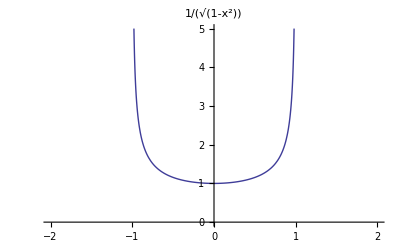

```mathematica
Plot[(1-x^2)^(-1/2),{x,-2,2},PlotLabel->(1-x^2)^(-1/2),PlotRange->{0,5}]
```

```mathematica
Mathematica indicates that the limit is complex infinity, even though observation of the function seems to lead to the conclusion that the limit should converge to 1.
```

```mathematica
Limit[(1-x^2)^(-1/2),x->1]
```

(-ⅈ) ∞

```mathematica
Looking at the left-hand and right-hand limits are not encouraging and suggest that the limit does not exist since they are unequal (complex infiniti and real infiniti, respectively)
```

```mathematica
Limit[(1-x^2)^(-1/2),x->1,Direction->1]
```

∞

```mathematica
Limit[(1-x^2)^(-1/2),x->1,Direction->-1]
```

(-ⅈ) ∞

```mathematica
The left and right-hand limits are non-0identical, so the limit should not exist from the basic calculus standpoint.  However, mathematica is taking into account higher mathematical knowledge of the complex plane and showing that the limit diverges.  For the purpose of this exam, it is safe to say that the limit is 1.
```

```mathematica
Problem 3:
```

```mathematica
The following function, denoted here as f, describes the fraction of surface coverage and is referred to as the Langmuir isotherm and comes about from solving the Hill-Landmuir equation. It is a specific case of an ideal-lattice-gas equation (Intro. to Chem. Eng. Thermodynamics by Smith, van Ness and Abbott). An alternative to this equation is the Freundlich equation. Langmuir isotherms can be derived from equilibrium kinteics of filled and unfilled sites as a function of the adsorption constant,a.  This constant essentially specifies the stability of the system that is gained by adsorbing a molecule.  The isotherm denotes the fraction of sites filled at a given temperature as a function of the system pressure (partial or total) or concentration.  The stability could be in terms of Gibb's Free Energy or other parameters, but the need to fill sites will be driven by the energy available at a certain temperature.  The value of a increases with the binding energy of the particle adsorbed onto the site and with decreasing T.
```

```mathematica
The Langmuir isotherm can also be derived from a Statistical Mechanics ensamble of m sites with n particles as a function of temperature.The temperature dependence likely has an equilibrium or rate constant controlled by a Boltzman, exponential of the binding energy and temperature.
```

```mathematica
f[x_]=(a*x)/(1+a*x)
```

(a x)/(1+a x)

```mathematica
f[a_,x_]=(a*x)/(1+a*x)
```

(a x)/(1+a x)

```mathematica
f[0,1]
```

0

```mathematica
f[1,0]
```

0

```mathematica
f[1,1]
```

1/2

```mathematica
Plot3D[f[a,x],{a,0,5},{x,0,100},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Plot3D[f[a,x],{a,0,5},{x,0,5},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Part A:
```

```mathematica
The codomain of this function as a function of a is given by [0,1].
```

```mathematica
For a specific upper bound of the function at a given pressure or concentration, see the following line of code.
```

```mathematica
Manipulate[f[a,x],{x,0,10}]
```

```mathematica
This plot establishes the upper bound on f for a given a value of x and is implied by the curve above.
```

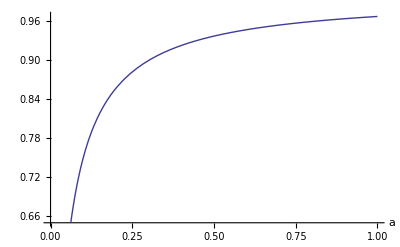

```mathematica
Plot[f[a,30],{a,0,1},AxesLabel->Automatic]
```

```mathematica
The codomain of a is indeed a subset of ℜ, since ℜ includes all real numbers (including positives, negatives, zero, rationals and irrationals).
```

```mathematica
For personal curiosity the first derivatives with respect to a and x are calculated.
```

```mathematica
D[(a x)/(1+a x),x]
```

-(a^2 x)/(1+a x)^2+a/(1+a x)

```mathematica
D[(a x)/(1+a x),a]
```

-(a x^2)/(1+a x)^2+x/(1+a x)

```mathematica
Part B:
```

```mathematica
In the zero limit, the value of f goes to zero.  This means, simply, that as the partial/total pressure of the system goes to zero, that the fraction of filled sites goes to zero as well. Again, a is the adsorption constant and determines the fraction of sites that are filled as a function of concentration or pressure in a particular system.  It's value does not come from this analysis however.
```

```mathematica
Limit[f[x],x->0]
```

0

```mathematica
Part C:
```

```mathematica
As the pressure or concentration of a species in solution gets very very high, all of the sites will be filled so the fraction of sites filled would be 1.  This is the case of full monolayer coverage.  There are other forms of the Langmuir isotherm that have saturation values less than one as related to the Henry's Law constant or other laws (Toth equation).
```

```mathematica
Limit[(a*x)/(1+a*x),x->∞]
```

1

```mathematica
For more arbitrary cases, the Langmuir isotherm can approach the saturation limit, m, in infinite pressure limit, so long as the isotherm fas the form:
```

```mathematica
f=(m*x)/(m/k+x)
```

```mathematica
where k is the Henry's constant and m is the total number of sites instead of the fraction of sites.
```

```mathematica
Part D:
```

```mathematica
The inverse function is defined such that when the function and its inverse are applied to one another in each order, the identity element, x, is output.
```

```mathematica
Testing a trial inverse function to see if it rearranges appropriately.
```

```mathematica
Solve[y==x/(a(1-x)),x]
```

{{x→(a y)/(1+a y)}}

```mathematica
Solving for the inverse function from the original function:
```

```mathematica
Solve[y==f[x],x]
```

{{x→-y/(a (-1+y))}}

```mathematica
finv[x_]=x/(a(1-x));
```

```mathematica
Applying the function and its inverse to themselves in sequential orderings:
```

```mathematica
FullSimplify[finv[f[x]]]
```

x

```mathematica
FullSimplify[f[finv[x]]]
```

x

```mathematica
This function, finv[x], passes all of the tests for an inverse function.
```

```mathematica
Part E:
```

```mathematica
f is continuous and infinitely differentiable with respect to x and a over the domain of [0,∞].Since negative pressures and concentrations do not make physical sense for the sytem of interest, they have been neglected from the domin, although the function's described properties may be extended over the domain.
```

```mathematica
Part F:
```

```mathematica
It is not clear that this integral has any physical meaning other than being the area under the curve of the function given, which is not the same as the integral of the Langmuir isotherm!  This is however, useful, in cmoputing the spreading pressure, ∏ (not the infinite product operator).  See p. 610 of van Abbott to interrelate that calculation to this one.
```

```mathematica
∫_0^(a*x) z/(1+z)ⅆz
```

ConditionalExpression[a x-Log[1+a x],Re[1/(a x)]≥0||Re[1/(a x)]≤-1||1/(a x)∉Reals]

```mathematica
This integral gives a count of all of the fraction of sites that have been occupied as the pressure or concentration increases to a certain value from no sites occupied.
```

```mathematica
∫_0^x (a*z)/(1+a*z)ⅆz
```

ConditionalExpression[(a x-Log[1+a x])/a,Re[1/(a x)]≥0||Re[1/(a x)]≤-1||1/(a x)∉Reals]

```mathematica
func[x_,a_]=a *x-Log[1+a* x]
```

a x-Log[1+a x]

```mathematica
Plot3D[func[x,a],{x,0,100},{a,0,1},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
Limit[func[x],x->0]
```

0

```mathematica
Problem 4:
```

```mathematica
Clear[n]
```

```mathematica
This entropy fundamental equation is not for an ideal gas, which scales as the Log[V/N] and the Log[U^(3/2)].  This can also be rewritten in terms of temperature.  Based  upon the differential form given, chemical potential is not a factor, otherwise there would have been a sum over the number of particles (as it would be in a more complete/realistic ensamble).  Therefore, it is assumed that the number of particles is held constant (if it weren't then Subscript[((∂S)/(∂N)), V,E]=-μ/T).
```

```mathematica
S[V_,U_]=(R^2/(θ*Subscript[υ, 0]))(n*V*U)^(1/3);
```

```mathematica
There are at least two approaches to this problem.  One could take the partial derivative of S in the, holding U and N constant.  Then equate this relationship with the one in the problem statement regarding (P/T).Since when U is fixed, T is fixed (or even if it weren't T would vary in a calculable way with respect to U).  Then multiply both sides by T and V.  It is important to note that we did not assume that V is constant, but for whichever change in S due to the change in V is picked the ratio of P/T.  This will give the result.  Furthermore, N is held constant as the box is assumed to be enclosed.  Assume that the constants R, υ0, θ are constant with respect to P,V, T, N, U, and S.
```

```mathematica
First, take the particl derivative with respect to V:
```

```mathematica
D[S[V,U],V]
```

(n R^2 U)/(3 (n U V)^(2/3) θ υ_0)

```mathematica
Knowing that this partial derivative is equal to  P/T, multiply both sides by T to get P:
```

```mathematica
D[S[V,U],V]*T
```

(n R^2 T U)/(3 (n U V)^(2/3) θ υ_0)

```mathematica
The following is the key relation that implies the solution to this problem.  In order to complete the problem, U or T must be eliminated from the equation.  It is the immediate line prior to this cell multiplied by V.
```

```mathematica
PV[V_,U_]=Simplify[D[S[V,U],V]*T*V]
```

(R^2 T (n U V)^(1/3))/(3 θ υ_0)

```mathematica
The unsimplified version of the above line just has the n*U*V term in the denominator
```

```mathematica
D[S[V,U],V]*T*V
```

(n R^2 T U V)/(3 (n U V)^(2/3) θ υ_0)

```mathematica
This next line is equal to 1/T, by definition, and is derived from the partial derivative of S with respect to U.
```

```mathematica
Simplify[D[S[V,U],U]]
```

(n R^2 V)/(3 (n U V)^(2/3) θ υ_0)

```mathematica
The following line is equal to T and will allow for substitution in the partial dericative of S w.r.t. V such that it may be expressed in terms of solely the intensive or extensive variables:
```

```mathematica
Simplify[1/D[S[V,U],V]]
```

(3 V θ υ_0)/(R^2 (n U V)^(1/3))

```mathematica
The negative root is ignored here since temperature  is proportional to the average kinetic energy of the system, it cannot take a negative value.
```

```mathematica
Solve[Simplify[D[S[V,U],U]]==(1/T),T]
```

{{T→(3 (n U V)^(2/3) θ υ_0)/(n R^2 V)}}

```mathematica
T is defined as:
```

```mathematica
(3 (n U V)^(2/3) θ Subscript[υ, 0])/(n R^2 V)
```

```mathematica
P[V,(3 (n U V)^(2/3) θ Subscript[υ, 0])/(n R^2 V)]
```

(R^2 T (((n U V)^(2/3) θ υ_0)/R^2)^(1/3))/(3^(2/3) θ υ_0)

```mathematica
T is then eliminated and the product PV is equal to the enthalpy of the system:
```

```mathematica
(R^2*(3 (n* U *V)^(2/3) *θ* Subscript[υ, 0])/(n* R^2 *V) *(n *U* V)^(1/3))/(3* θ *Subscript[υ, 0])
```

U

```mathematica
FullSimplify[(R^2*(3 (n U V)^(2/3) θ Subscript[υ, 0])/(n R^2 V)* (n* U* V)^(1/3))/(3 *θ* Subscript[υ, 0])]
```

U

```mathematica
The following line of code determines the enthalpy of the system in terms of the state variables T,V,R,etc. and is an alternative expression for PV.  The positive square root is considered.
```

```mathematica
Solve[Simplify[D[S[V,U],U]]==(1/T),U]
```

{{U→-(√n R^3 T^(3/2) √V)/(3 √3 θ^(3/2) υ_0^(3/2))},{U→(√n R^3 T^(3/2) √V)/(3 √3 θ^(3/2) υ_0^(3/2))}}

```mathematica
PV[V,U]/S[V,U]
```

T/3

```mathematica
So PV is also equivalent to (TS/3).  So P*V=(T*S[V,U])/3=U=((√n R^3 T^(3/2) √V)/(3 √3 θ^(3/2) Subscript[υ, 0]^(3/2))).
```

```mathematica
U is defined as:
```

```mathematica
(√n R^3 T^(3/2) √V)/(3 √3 θ^(3/2) Subscript[υ, 0]^(3/2))
```

```mathematica
For some reason, Mathematica is not simplifying the following results as expected.
```

```mathematica
(R^2* T* (n *(√n * R^3* T^(3/2)* √V)/(3 √3* θ^(3/2)* Subscript[υ, 0]^(3/2)) *V)^(1/3))/(3* θ *Subscript[υ, 0])
```

(R^2 T ((n^(3/2) R^3 T^(3/2) V^(3/2))/(θ^(3/2) υ_0^(3/2)))^(1/3))/(3 √3 θ υ_0)

```mathematica
FullSimplify[(R^2* T *((√n* R^3* T^(3/2)* √V)/(3 √3* θ^(3/2)* Subscript[υ, 0]^(3/2)))^(1/3))/(3* θ* Subscript[υ, 0])]
```

(R^2 T ((√n R^3 T^(3/2) √V)/(θ^(3/2) υ_0^(3/2)))^(1/3))/(3 √3 θ υ_0)

```mathematica
Extra work:
```

```mathematica
A second method involves the following relation: P=(Subscript[((∂S)/(∂V)), N,U]/Subscript[((∂S)/(∂U)), N,V]).  These are both calculable and can be substituted in based upon the "fundamental relation" and then multiplied by V.
```

```mathematica
D[S[V,U],V]
```

(n R^2 U)/(3 (n U V)^(2/3) θ υ_0)

```mathematica
D[S[V,U],U]
```

(n R^2 V)/(3 (n U V)^(2/3) θ υ_0)

```mathematica
D[S[V,U],V]/D[S[V,U],U]
```

U/V

```mathematica
This is the solution computed before:
```

```mathematica
D[S[V,U],V]/D[S[V,U],U]*V
```

U

```mathematica
Solve[S[V,U]==Entro,U]
```

{{U→(Entro^3 θ^3 υ_0^3)/(n R^6 V)}}

```mathematica
D[(S^3 θ^3 Subscript[υ, 0]^3)/(n R^6 V),V]
```

-(S^3 θ^3 υ_0^3)/(n R^6 V^2)

```mathematica
-1*D[(S^3 θ^3 Subscript[υ, 0]^3)/(n R^6 V),V]
```

(S^3 θ^3 υ_0^3)/(n R^6 V^2)

```mathematica
-1*D[(S^3 θ^3 Subscript[υ, 0]^3)/(n R^6 V),V]*V
```

(S^3 θ^3 υ_0^3)/(n R^6 V)

```mathematica
This is the U value calculated above.
```

```mathematica
Another method involves solving the fundamental relation for U and then using the fact that P=-Subscript[((∂U)/(∂V)), N,S].
```

```mathematica
Another method involves incorporating the rules of implicit differentiation and the chain rule for S and some transformations.
```

```mathematica
S^3
```

(n R^6 U V)/(θ^3 υ_0^3)

```mathematica
The heat capacity can also be calculated easily from T * ds/dT at constant P.
```

```mathematica
Problem 5:
```

```mathematica
Part A:
```

```mathematica
The continuity equation in ℝ^3 is a result of writing a maass balance around a finite volume element Δx ΔyΔz.  The left hand side is ΔxΔyΔz(dρ/dt) and the right hand side comes from evaluating the area and the density multiplied by velocity of flow parallel to the surfaces of a cube in that direction.  Division by the volume element xΔΔyΔz and taking the limit as theΔ volume element goes to zero produces the continuity equation.  It relates the change in fluid density of a fixed point in space.  Then the terms are rearranged to be equal to zero.  This derivation is fully developed in Bird, Stewart and Lightfoot Chapter 3 (Wiley 2007).There are no other physical properties of the system to consider in this simple case.
```

```mathematica
The continuity equation and associated mathematics are based upon our ability to treat a group of atoms in a localized volume (epsilon neighborhood) as a single point with group properties.  The legnthscale at which we can no longer treat a group of atoms as a single point is approx. 100 nm regime.  Brownian motion and their random-walk, probabalistic motions are not predicted by the typical continuity equation. This greatly simplifies the mathematics governing fluid motions.  It would not be possible to perform molecular dynamics simulations that treat every atom and molecule in deriving parabolc velocity profiles in a pipe, for example.
The concept of a continuum is a fundamental and axiomatic generalization.  In a continum, the sizescale of the neigborhood is important: too small and the mathematics of molecular motion is necessary and at too large a size scale, it is easier to conisder averages, but there is a loss in specificity.  Scalar, tensor and vector calculus allow us to interrelate the two.
The way that the continuity equation is written in this specific problem has the density outside of the ∇ operator.  Therefore, differential equations governed by phenomena wherein the local density can change as a function o f an applied external force will not bo governed by the 'usual' transport equations.  Such is the case inside of pumps, nucleation and growth of liquid crystals, motions of particles due to Brownian motion (discernable via microscope), Marangoni effects and wine tears, interferance patterns in molecular motion that define Bose-Einstein condensates.
```

```mathematica
The transport equations do contain more properties of the species that are localized to volumes.
```

```mathematica
The usualy transport equations also fail when flow is not fully developed or is turbulent or is not plug-flow.
```

```mathematica
Part B:Group theory refers to the mathematical constructions concerning rings, fields, vector spaces as well as the peripheral mathematics that supports them.  Many of the functions that it characterizes possess certain symmetries or assymmetries that are understood in harmonic analyses.  These same harmonic anlyses often are useful in solving partial differential equations.

Strong coupling of interaction forces can lead to interfacial tensions that alter flow behavior and are not predicted by transport equations.  

A Derivation of the Nonlocal Volume-Averaged Equations for Two-Phase Flow Transport.
When the temperatures and pressures are in such extremes that other material properties of interest such as volumetric expension, solubility /miscibility, resistivity, vapor pressure, and other properties are not constant over the volume elements of interest.
```

```mathematica
Group theory allows engineers to treat a finite, small and differential volume as a collective unit that has simmilar, well-defined properties.  In the finite limit, a control volume, the relevant parameters are considered and a balance of some sort takes place.A balance at various boundary conditions creates a differential form that can then be sovled with appropriate mathematics.
```

```mathematica
The mathematics of constructing transport equations that do depend on the properties of various materials involves tensor calculus.  After deriving the full tensor description of the problem at hand, then assumptions about the symmetry in the governing tensor can be applied and reduce the number of coefficents or equations that must be solved in order to gain understanding of the phenomena the equatons explain.  Some of the assumptions to simplify the tensors might by: symmetry, isotropy.
```

```mathematica
The falling film equation is an example of an equation that can lead to these size scales.  Therefore, the fluxes and reations involving falling films require special care.
```

```mathematica
Compressible fluids might create unusual transport equations. Non-newtonian fluids also possess unusual transport equations.
```

```mathematica
Symmetry can often times simplify problems greatly.  An example of this is the relationship between the stress tensor and the stress tensor.
```

```mathematica
σ^ij=-ρ*g^ij+k^ijpq Subscript[u, pq]+O(u*pq^2)
```

```mathematica
By ignoring the higher order terms, which many statistical mechanics people will not, the problem becomes much simpler to solve for the appropriate constitutive equation.  From 81 coefficients, to 36 (symmetric tensor assumption... Subscript[u, ij]=Subscript[u, ji] ji)to 21 (k^ijpq=k^pqij).  Without group theory, these interrelationships would not be possible.
```

```mathematica
σ^ij=-ρ*g^ij+k^ijpq Subscript[u, pq]
```

```mathematica
In the sense that, isotropy can decrease the number of tensor elements necessary for consideration.
```

```mathematica
For an example of a specific equation, utilize the example of Flow near a Wall Suddenly Set in Motion (Bird, Stewart, Lightfoot, Ch4, Ex. 4.1-1).  The governing differential equation is developed from finite volume approaches, then boundary conditions are specified and the appropriate solution is discovered.  The additional property of the system, other than velocity and density, is viscosity.  Group theory implies that the local velocity, viscosity and density are coupled to the volumes of interest in space. Instead of being attributed directly to molecules themselved, because there would be more variables than possible to solve for arbitrary size scales, timescale and of interest.
```

```mathematica
The same is true for parabolic (or other) velocity profiles inside pipes.
```

```mathematica
Part C:
```

```mathematica
Statistical Mechanics is helpful in defining systems wherein the expectation value of a system is most important and all of the minor fluctuations can be ignored.  It is useful in looking at systems where the energy of mulecular interactions is on the order of magnitude of kBT or less.It has significant implications where analogies can be made between the system of interest and a gas- electrons in semiconductors,band gaps, fermi levels, plasma behavior, etc.  It allows for the estimation of macroscopic equations that explain measureable properties of the system from a basis of intramolecular interactions.
```

```mathematica
Molecular dynamics (including solutions, surface interactions) utilizes ensamble theories to preduct molecular motion.
```